## Load Radia

```mathematica
<<Radia`;
RadPlot3DOptions[];
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

## Load Insertion Device Functions

Open and evaluate the notebook “IDFunctions.nb”

## Set Directory

```mathematica
SetDirectory["C:\\Users\\luana.vilela\\Desktop\\ondulador_kyma\\Simulation\\2020-05-11_Kickmaps_APUKyma22mm"];
```

## APU Kyma 22mm

```mathematica
(*ID parameters*)
λu = 22; (*Period [mm]*)
Np = 52; (*Number of periods (not including terminations)*)
Br = 1.32; (*Remanent magnetization [T]*)
gap = 8;
BlockGap = 0.1;
Termination = "ThreeBlocksAntiSym"; 

(*Longitudinal range [mm]*)
Lstep = 0.5;
Li = -800;
Lf = 800;
Lnpts =Round[(Lf - Li)/Lstep ]+ 1; 

(*Horizontal range [mm]*)
Hstep =1;
Hi = -13;
Hf = 13;
Hnpts = Round[(Hf - Hi)/Hstep ]+ 1; 

(*Vertical range [mm]*)
Vstep =0.45;
Vi = -3.6;
Vf = 3.6;
Vnpts = Round[(Vf - Vi)/Vstep ]+ 1; 

(*Particle energy [GeV]*)
Energy = 3;

(*Radia randomization magnitudes*)
radFldLenTol[10^-12,10^-12 ];

idname="APUKyma22mm";
```

## Kickmap Shift 0

Shift: 0 [mm]

IDAPU: elapsed time = 0.7031104 s

-Graphics3D-

IDShow: elapsed time = 0.8437541 s

Horizontal field amplitude:    2.23328×10^-9 [T]

Vertical field amplitude:      0.740993 [T]

Longitudinal field amplitude:  2.40831×10^-11 [T]

Horizontal K: 1.52259

Vertical K:   4.58893×10^-9

IDInfo: elapsed time = 0.328124 s

IDPlotFields: elapsed time = 11.437464 s

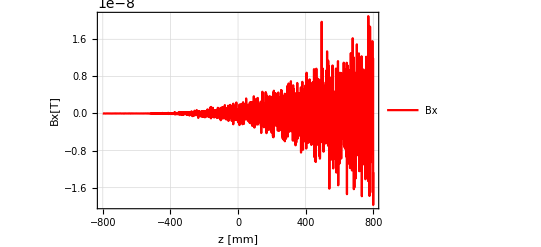
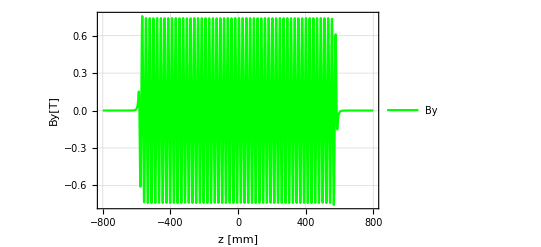
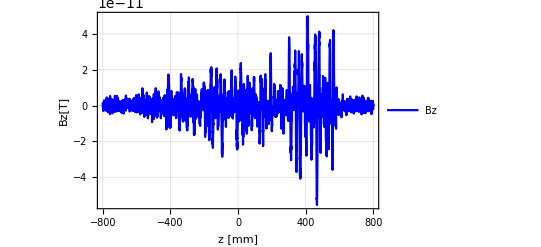

Fieldmap saved in file: APUKyma22mm_fieldmap_shift_0.txt

IDFieldMap: elapsed time = 120.718455 s

Kickmap saved in file: APUKyma22mm_kickmap_shift_0.txt

Kickmap calculated in: 27.2 min

```mathematica
δP = 0;
Print["Shift: ",  δP, " [mm]"];

fieldmapfilename = StringTemplate["`1`_fieldmap_shift_`2`.txt"][idname, δP];
kickmapfilename = StringTemplate["`1`_kickmap_shift_`2`.txt"][idname, δP];

APU = IDAPU[λu, Np, Br, gap, "δP" -> δP, "BlockGap"-> BlockGap,"Termination" -> Termination];
IDShow[APU]
IDInfo[APU, λu]
IDPlotFields[APU, "z", {Li, Lf}]

IDFieldMap[fieldmapfilename, APU, {Hi, Hf}, {0, 0}, {Li,Lf}, Hnpts, 1, Lnpts ] ;

t0=AbsoluteTime[];
Results = radFldFocKick[APU,{0.0,0.0,Li},{0,0,1},{(Lf-Li)},Lnpts,{1,0,0},(Hf-Hi),Hnpts,(Vf-Vi),Vnpts,"",{0,0}];
t1=AbsoluteTime[];
Export[kickmapfilename, Results[[4]]];
Print["Kickmap saved in file: ",kickmapfilename];
Print["Kickmap calculated in: ",Round[t1-t0]/60.0," min"];
```

## Kickmap Shift λu/8

Shift: 11/4 [mm]

IDAPU: elapsed time = 0.437498 s

-Graphics3D-

IDShow: elapsed time = 0.749998 s

Horizontal field amplitude:    2.50228×10^-9 [T]

Vertical field amplitude:      0.686552 [T]

Longitudinal field amplitude:  0.280848 [T]

Horizontal K: 1.41073

Vertical K:   5.14169×10^-9

IDInfo: elapsed time = 0.343757 s

IDPlotFields: elapsed time = 10.734323 s

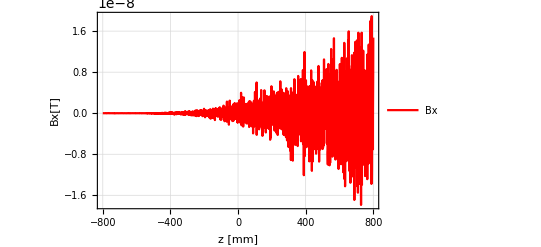
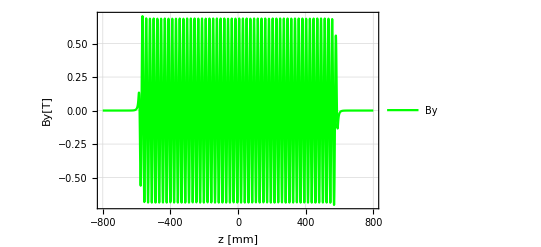
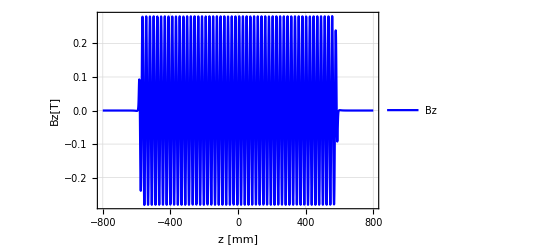

Fieldmap saved in file: APUKyma22mm_fieldmap_shift_2.75.txt

IDFieldMap: elapsed time = 121.985454 s

Kickmap saved in file: APUKyma22mm_kickmap_shift_2.75.txt

Kickmap calculated in: 27.1333 min

```mathematica
δP = λu/8;
Print["Shift: ",  δP, " [mm]"];

fieldmapfilename = StringTemplate["`1`_fieldmap_shift_`2`.txt"][idname, δP];
kickmapfilename = StringTemplate["`1`_kickmap_shift_`2`.txt"][idname, δP];

APU = IDAPU[λu, Np, Br, gap, "δP" -> δP, "BlockGap"-> BlockGap,"Termination" -> Termination];
IDShow[APU]
IDInfo[APU, λu]
IDPlotFields[APU, "z", {Li, Lf}]

IDFieldMap[fieldmapfilename, APU, {Hi, Hf}, {0, 0}, {Li,Lf}, Hnpts, 1, Lnpts ] ;

t0=AbsoluteTime[];
Results = radFldFocKick[APU,{0.0,0.0,Li},{0,0,1},{(Lf-Li)},Lnpts,{1,0,0},(Hf-Hi),Hnpts,(Vf-Vi),Vnpts,"",{0,0}];
t1=AbsoluteTime[];
Export[kickmapfilename, Results[[4]]];
Print["Kickmap saved in file: ",kickmapfilename];
Print["Kickmap calculated in: ",Round[t1-t0]/60.0," min"];
```

## Kickmap Shift λu/4

Shift: 11/2 [mm]

IDAPU: elapsed time = 0.4375192 s

-Graphics3D-

IDShow: elapsed time = 0.7656206 s

Horizontal field amplitude:    1.94825×10^-9 [T]

Vertical field amplitude:      0.526065 [T]

Longitudinal field amplitude:  0.52245 [T]

Horizontal K: 1.08096

Vertical K:   4.00327×10^-9

IDInfo: elapsed time = 0.343731 s

IDPlotFields: elapsed time = 10.890619 s

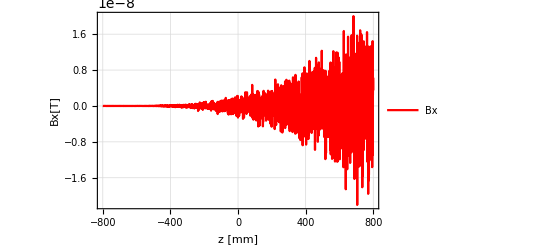
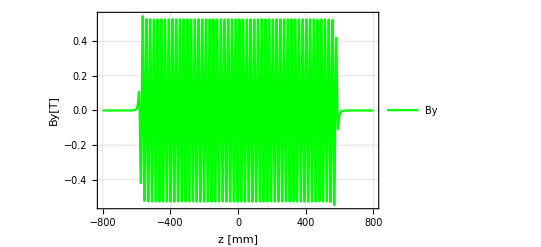
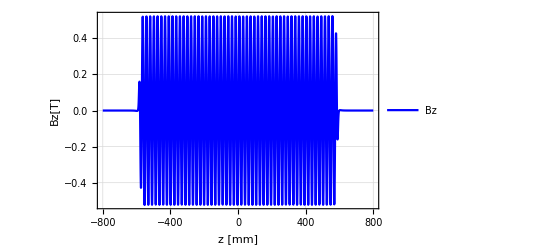

Fieldmap saved in file: APUKyma22mm_fieldmap_shift_5.5.txt

IDFieldMap: elapsed time = 121.782775 s

Kickmap saved in file: APUKyma22mm_kickmap_shift_5.5.txt

Kickmap calculated in: 26.9833 min

```mathematica
δP = λu/4;
Print["Shift: ",  δP, " [mm]"];

fieldmapfilename = StringTemplate["`1`_fieldmap_shift_`2`.txt"][idname, δP];
kickmapfilename = StringTemplate["`1`_kickmap_shift_`2`.txt"][idname, δP];

APU = IDAPU[λu, Np, Br, gap, "δP" -> δP, "BlockGap"-> BlockGap,"Termination" -> Termination];
IDShow[APU]
IDInfo[APU, λu]
IDPlotFields[APU, "z", {Li, Lf}]

IDFieldMap[fieldmapfilename, APU, {Hi, Hf}, {0, 0}, {Li,Lf}, Hnpts, 1, Lnpts ] ;

t0=AbsoluteTime[];
Results = radFldFocKick[APU,{0.0,0.0,Li},{0,0,1},{(Lf-Li)},Lnpts,{1,0,0},(Hf-Hi),Hnpts,(Vf-Vi),Vnpts,"",{0,0}];
t1=AbsoluteTime[];
Export[kickmapfilename, Results[[4]]];
Print["Kickmap saved in file: ",kickmapfilename];
Print["Kickmap calculated in: ",Round[t1-t0]/60.0," min"];
```

## Kickmap Shift 3λu/8

Shift: 33/4 [mm]

IDAPU: elapsed time = 0.4218675 s

-Graphics3D-

IDShow: elapsed time = 0.7343853 s

Horizontal field amplitude:    1.85501×10^-9 [T]

Vertical field amplitude:      0.282757 [T]

Longitudinal field amplitude:  0.681697 [T]

Horizontal K: 0.581009

Vertical K:   3.81168×10^-9

IDInfo: elapsed time = 0.328113 s

IDPlotFields: elapsed time = 10.640601 s

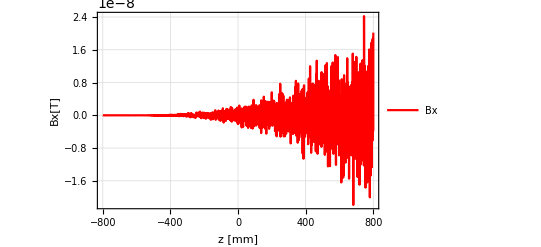
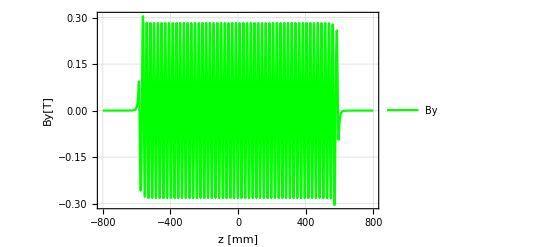
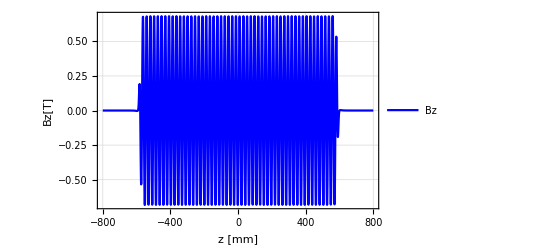

Fieldmap saved in file: APUKyma22mm_fieldmap_shift_8.25.txt

IDFieldMap: elapsed time = 121.579087 s

Kickmap saved in file: APUKyma22mm_kickmap_shift_8.25.txt

Kickmap calculated in: 26.95 min

```mathematica
δP = 3λu/8;
Print["Shift: ",  δP, " [mm]"];

fieldmapfilename = StringTemplate["`1`_fieldmap_shift_`2`.txt"][idname, δP];
kickmapfilename = StringTemplate["`1`_kickmap_shift_`2`.txt"][idname, δP];

APU = IDAPU[λu, Np, Br, gap, "δP" -> δP, "BlockGap"-> BlockGap,"Termination" -> Termination];
IDShow[APU]
IDInfo[APU, λu]
IDPlotFields[APU, "z", {Li, Lf}]

IDFieldMap[fieldmapfilename, APU, {Hi, Hf}, {0, 0}, {Li,Lf}, Hnpts, 1, Lnpts ] ;

t0=AbsoluteTime[];
Results = radFldFocKick[APU,{0.0,0.0,Li},{0,0,1},{(Lf-Li)},Lnpts,{1,0,0},(Hf-Hi),Hnpts,(Vf-Vi),Vnpts,"",{0,0}];
t1=AbsoluteTime[];
Export[kickmapfilename, Results[[4]]];
Print["Kickmap saved in file: ",kickmapfilename];
Print["Kickmap calculated in: ",Round[t1-t0]/60.0," min"];
```

## Kickmap Shift λu/2

Shift: 11 [mm]

IDAPU: elapsed time = 0.4218698 s

-Graphics3D-

IDShow: elapsed time = 0.7656206 s

Horizontal field amplitude:    2.55249×10^-9 [T]

Vertical field amplitude:      1.91297×10^-9 [T]

Longitudinal field amplitude:  0.735616 [T]

Horizontal K: 3.93076×10^-9

Vertical K:   5.24485×10^-9

IDInfo: elapsed time = 0.32813 s

IDPlotFields: elapsed time = 10.187471 s

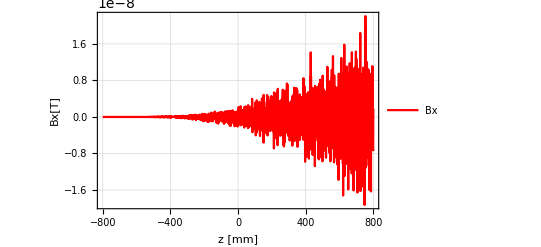
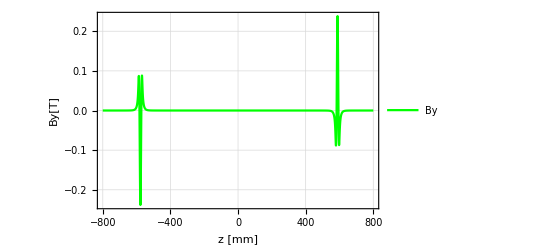
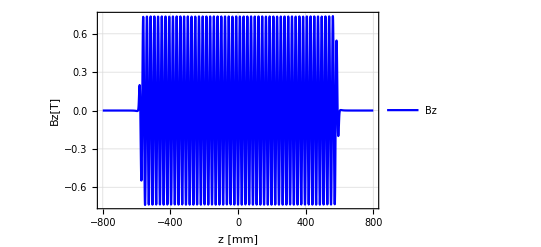

Fieldmap saved in file: APUKyma22mm_fieldmap_shift_11.txt

IDFieldMap: elapsed time = 122.234036 s

Kickmap saved in file: APUKyma22mm_kickmap_shift_11.txt

Kickmap calculated in: 27.0833 min

```mathematica
δP = λu/2;
Print["Shift: ",  δP, " [mm]"];

fieldmapfilename = StringTemplate["`1`_fieldmap_shift_`2`.txt"][idname, δP];
kickmapfilename = StringTemplate["`1`_kickmap_shift_`2`.txt"][idname, δP];

APU = IDAPU[λu, Np, Br, gap, "δP" -> δP, "BlockGap"-> BlockGap,"Termination" -> Termination];
IDShow[APU]
IDInfo[APU, λu]
IDPlotFields[APU, "z", {Li, Lf}]

IDFieldMap[fieldmapfilename, APU, {Hi, Hf}, {0, 0}, {Li,Lf}, Hnpts, 1, Lnpts ] ;

t0=AbsoluteTime[];
Results = radFldFocKick[APU,{0.0,0.0,Li},{0,0,1},{(Lf-Li)},Lnpts,{1,0,0},(Hf-Hi),Hnpts,(Vf-Vi),Vnpts,"",{0,0}];
t1=AbsoluteTime[];
Export[kickmapfilename, Results[[4]]];
Print["Kickmap saved in file: ",kickmapfilename];
Print["Kickmap calculated in: ",Round[t1-t0]/60.0," min"];
```